```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=10;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

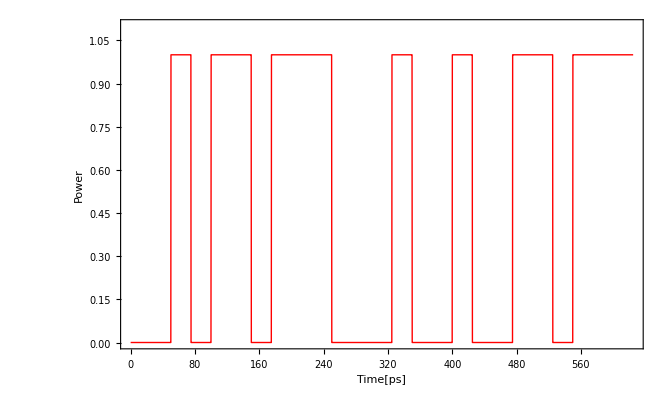

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->30},PlotRange->{0,1.1}]
```

1/2 (1+Cos[400000000000000 π t])

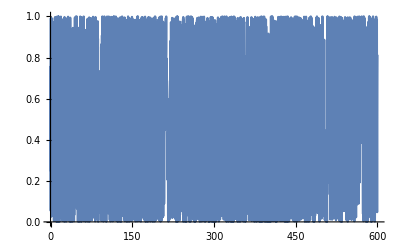

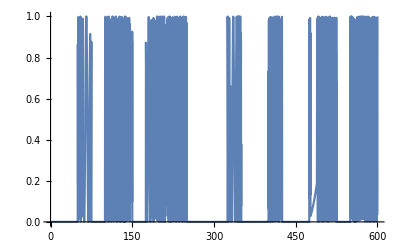

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t_]= (1+Cos[2*Pi*Fc*t])/2
Plot[carrier[t], {t,0,600}]
cs[t_]:=signal[t]*carrier[t]
Plot[cs[t*10^-12],{t,0,600}]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))
```

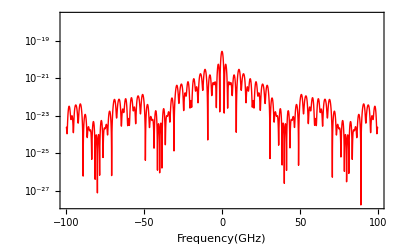

```mathematica
LogPlot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-19}]
```

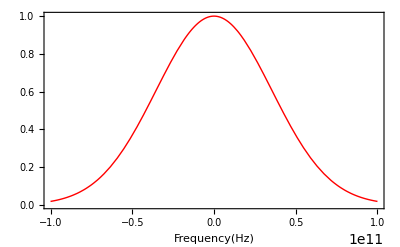

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

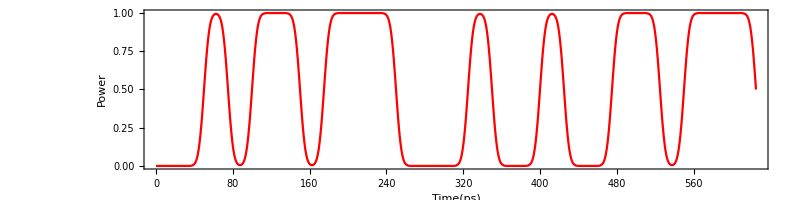

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

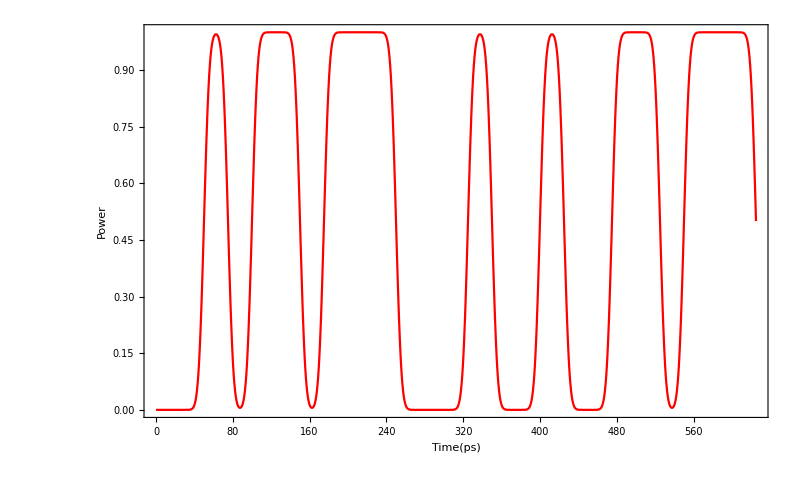

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->40,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
f[x_]:=1/(√(2*Pi*β2*L))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*L)-Pi/4)];
```

```mathematica
FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]
```

{2.79363×10^16,{x1→0.873066}}

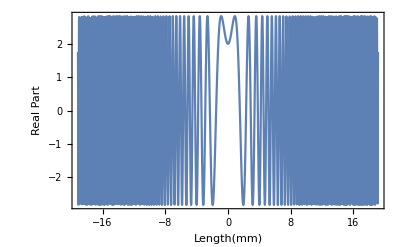

```mathematica
max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]
```

## Impulse Responce for Fiber Dispersion

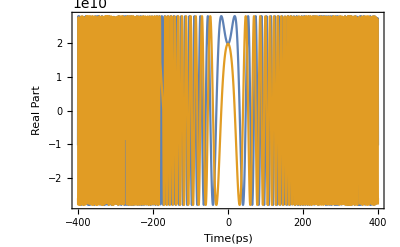

```mathematica
hdis[t_]:=1/(√(2*Pi*β2*L))*Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
hcmp[t_]:=
(*1/(√(2*Pi*β2*80))*10^6*)Exp[+ⅈ*(t^2/(2*β2*L)-Pi/4)];
```

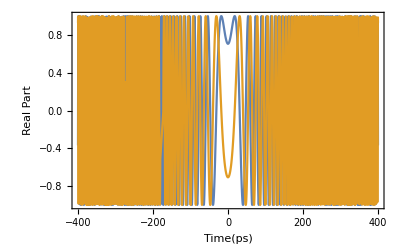

```mathematica
Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]
```

```mathematica
IntegerPart[total*10^12]
```

784

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

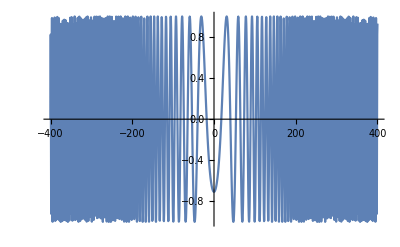

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

## Simulation

```mathematica
simu0[a_]:=simu0[a]=Sum[hdis2[z]*hcmp3[a-z],{z,-10000,10000,samp}]
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*simu0[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

-1.53094×10^11-2.88525×10^11 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,3.26626×10^11},{-99.5,3.65618×10^11},{-99.,4.04202×10^11},{-98.5,4.4188×10^11},{-98.,4.78102×10^11},{-97.5,5.12316×10^11},{-97.,5.44032×10^11},{-96.5,5.72843×10^11},{-96.,5.98431×10^11},{-95.5,6.2054×10^11},{-95.,6.38985×10^11},{-94.5,6.53671×10^11},{-94.,6.64637×10^11},{-93.5,6.72077×10^11},{-93.,6.7635×10^11},{-92.5,6.77956×10^11},{-92.,6.77531×10^11},{-91.5,6.75839×10^11},{-91.,6.73764×10^11},{-90.5,6.72272×10^11},{-90.,6.72342×10^11},{-89.5,6.74884×10^11},{-89.,6.80665×10^11},{-88.5,6.90266×10^11},{-88.,7.04041×10^11},{-87.5,7.22083×10^11},{-87.,7.44201×10^11},{-86.5,7.69937×10^11},{-86.,7.98624×10^11},{-85.5,8.29486×10^11},{-85.,8.6172×10^11},{-84.5,8.94544×10^11},{-84.,9.27212×10^11},{-83.5,9.59023×10^11},{-83.,9.89351×10^11},{-82.5,1.01768×10^12},{-82.,1.04362×10^12},{-81.5,1.06693×10^12},{-81.,1.0875×10^12},{-80.5,1.10529×10^12},{-80.,1.12038×10^12},{-79.5,1.13292×10^12},{-79.,1.14317×10^12},{-78.5,1.15147×10^12},{-78.,1.15823×10^12},{-77.5,1.16391×10^12},{-77.,1.16899×10^12},{-76.5,1.17396×10^12},{-76.,1.17934×10^12},{-75.5,1.18562×10^12},{-75.,1.19327×10^12},{-74.5,1.20268×10^12},{-74.,1.21419×10^12},{-73.5,1.228×10^12},{-73.,1.24423×10^12},{-72.5,1.26284×10^12},{-72.,1.28367×10^12},{-71.5,1.30638×10^12},{-71.,1.33054×10^12},{-70.5,1.35559×10^12},{-70.,1.38092×10^12},{-69.5,1.40586×10^12},{-69.,1.42968×10^12},{-68.5,1.4517×10^12},{-68.,1.47126×10^12},{-67.5,1.48778×10^12},{-67.,1.50082×10^12},{-66.5,1.51004×10^12},{-66.,1.51526×10^12},{-65.5,1.51642×10^12},{-65.,1.51359×10^12},{-64.5,1.50701×10^12},{-64.,1.49705×10^12},{-63.5,1.48421×10^12},{-63.,1.46906×10^12},{-62.5,1.45224×10^12},{-62.,1.43441×10^12},{-61.5,1.41625×10^12},{-61.,1.39845×10^12},{-60.5,1.38164×10^12},{-60.,1.36642×10^12},{-59.5,1.35328×10^12},{-59.,1.34262×10^12},{-58.5,1.33476×10^12},{-58.,1.32988×10^12},{-57.5,1.32805×10^12},{-57.,1.32923×10^12},{-56.5,1.33328×10^12},{-56.,1.33992×10^12},{-55.5,1.34881×10^12},{-55.,1.35949×10^12},{-54.5,1.37145×10^12},{-54.,1.3841×10^12},{-53.5,1.39681×10^12},{-53.,1.40895×10^12},{-52.5,1.4199×10^12},{-52.,1.42904×10^12},{-51.5,1.43584×10^12},{-51.,1.43979×10^12},{-50.5,1.4405×10^12},{-50.,1.43768×10^12},{-49.5,1.43117×10^12},{-49.,1.42093×10^12},{-48.5,1.40703×10^12},{-48.,1.38963×10^12},{-47.5,1.36899×10^12},{-47.,1.34546×10^12},{-46.5,1.31942×10^12},{-46.,1.2913×10^12},{-45.5,1.26155×10^12},{-45.,1.23058×10^12},{-44.5,1.19879×10^12},{-44.,1.16652×10^12},{-43.5,1.13409×10^12},{-43.,1.10174×10^12},{-42.5,1.06967×10^12},{-42.,1.03802×10^12},{-41.5,1.00687×10^12},{-41.,9.76262×10^11},{-40.5,9.46196×10^11},{-40.,9.16655×10^11},{-39.5,8.87606×10^11},{-39.,8.59025×10^11},{-38.5,8.30918×10^11},{-38.,8.03345×10^11},{-37.5,7.76431×10^11},{-37.,7.50388×10^11},{-36.5,7.25521×10^11},{-36.,7.02243×10^11},{-35.5,6.81068×10^11},{-35.,6.62584×10^11},{-34.5,6.47408×10^11},{-34.,6.36103×10^11},{-33.5,6.29106×10^11},{-33.,6.2665×10^11},{-32.5,6.28717×10^11},{-32.,6.35017×10^11},{-31.5,6.45022×10^11},{-31.,6.5801×10^11},{-30.5,6.73145×10^11},{-30.,6.89555×10^11},{-29.5,7.064×10^11},{-29.,7.22925×10^11},{-28.5,7.38478×10^11},{-28.,7.52522×10^11},{-27.5,7.6462×10^11},{-27.,7.74429×10^11},{-26.5,7.81691×10^11},{-26.,7.86217×10^11},{-25.5,7.87866×10^11},{-25.,7.86542×10^11},{-24.5,7.82182×10^11},{-24.,7.74766×10^11},{-23.5,7.64321×10^11},{-23.,7.5094×10^11},{-22.5,7.34784×10^11},{-22.,7.16106×10^11},{-21.5,6.95273×10^11},{-21.,6.7278×10^11},{-20.5,6.49269×10^11},{-20.,6.25506×10^11},{-19.5,6.02375×10^11},{-19.,5.80827×10^11},{-18.5,5.61841×10^11},{-18.,5.46341×10^11},{-17.5,5.35097×10^11},{-17.,5.28646×10^11},{-16.5,5.27228×10^11},{-16.,5.30799×10^11},{-15.5,5.39063×10^11},{-15.,5.51555×10^11},{-14.5,5.67727×10^11},{-14.,5.87025×10^11},{-13.5,6.08954×10^11},{-13.,6.33085×10^11},{-12.5,6.59058×10^11},{-12.,6.8656×10^11},{-11.5,7.15312×10^11},{-11.,7.45063×10^11},{-10.5,7.75577×10^11},{-10.,8.06634×10^11},{-9.5,8.38024×10^11},{-9.,8.69574×10^11},{-8.5,9.0115×10^11},{-8.,9.32669×10^11},{-7.5,9.64084×10^11},{-7.,9.95379×10^11},{-6.5,1.02656×10^12},{-6.,1.05762×10^12},{-5.5,1.08854×10^12},{-5.,1.11927×10^12},{-4.5,1.14966×10^12},{-4.,1.17952×10^12},{-3.5,1.20859×10^12},{-3.,1.23656×10^12},{-2.5,1.26307×10^12},{-2.,1.28774×10^12},{-1.5,1.31019×10^12},{-1.,1.33009×10^12},{-0.5,1.34717×10^12},{0.,1.36123×10^12},{0.5,1.37218×10^12},{1.,1.38002×10^12},{1.5,1.38489×10^12},{2.,1.38699×10^12},{2.5,1.38664×10^12},{3.,1.38421×10^12},{3.5,1.38011×10^12},{4.,1.3748×10^12},{4.5,1.36875×10^12},{5.,1.36243×10^12},{5.5,1.35628×10^12},{6.,1.35074×10^12},{6.5,1.34618×10^12},{7.,1.34295×10^12},{7.5,1.34132×10^12},{8.,1.34149×10^12},{8.5,1.34354×10^12},{9.,1.3475×10^12},{9.5,1.35328×10^12},{10.,1.36068×10^12},{10.5,1.36944×10^12},{11.,1.37922×10^12},{11.5,1.38965×10^12},{12.,1.40036×10^12},{12.5,1.41097×10^12},{13.,1.42112×10^12},{13.5,1.43049×10^12},{14.,1.43881×10^12},{14.5,1.44585×10^12},{15.,1.45145×10^12},{15.5,1.45547×10^12},{16.,1.45785×10^12},{16.5,1.45859×10^12},{17.,1.45775×10^12},{17.5,1.45544×10^12},{18.,1.45187×10^12},{18.5,1.44724×10^12},{19.,1.44183×10^12},{19.5,1.43591×10^12},{20.,1.42971×10^12},{20.5,1.42345×10^12},{21.,1.41726×10^12},{21.5,1.4112×10^12},{22.,1.40527×10^12},{22.5,1.39942×10^12},{23.,1.39354×10^12},{23.5,1.38752×10^12},{24.,1.38123×10^12},{24.5,1.37461×10^12},{25.,1.36761×10^12},{25.5,1.3602×10^12},{26.,1.35239×10^12},{26.5,1.34419×10^12},{27.,1.33557×10^12},{27.5,1.32644×10^12},{28.,1.31664×10^12},{28.5,1.30589×10^12},{29.,1.29382×10^12},{29.5,1.27995×10^12},{30.,1.2638×10^12},{30.5,1.24484×10^12},{31.,1.22263×10^12},{31.5,1.19691×10^12},{32.,1.16764×10^12},{32.5,1.13509×10^12},{33.,1.09994×10^12},{33.5,1.0633×10^12},{34.,1.02677×10^12},{34.5,9.92442×10^11},{35.,9.62869×10^11},{35.5,9.41043×10^11},{36.,9.30383×10^11},{36.5,9.34811×10^11},{37.,9.59067×10^11},{37.5,1.00933×10^12},{38.,1.0942×10^12},{38.5,1.22572×10^12},{39.,1.42005×10^12},{39.5,1.69749×10^12},{40.,2.08192×10^12},{40.5,2.60017×10^12},{41.,3.2817×10^12},{41.5,4.15828×10^12},{42.,5.26374×10^12},{42.5,6.63323×10^12},{43.,8.30231×10^12},{43.5,1.03055×10^13},{44.,1.2675×10^13},{44.5,1.54384×10^13},{45.,1.86173×10^13},{45.5,2.22258×10^13},{46.,2.6268×10^13},{46.5,3.07378×10^13},{47.,3.56175×10^13},{47.5,4.08772×10^13},{48.,4.64758×10^13},{48.5,5.23609×10^13},{49.,5.84708×10^13},{49.5,6.4736×10^13},{50.,7.10817×10^13},{50.5,7.74301×10^13},{51.,8.37037×10^13},{51.5,8.98275×10^13},{52.,9.57321×10^13},{52.5,1.01356×10^14},{53.,1.06646×10^14},{53.5,1.11563×10^14},{54.,1.16075×10^14},{54.5,1.20167×10^14},{55.,1.23833×10^14},{55.5,1.27077×10^14},{56.,1.29913×10^14},{56.5,1.32365×10^14},{57.,1.3446×10^14},{57.5,1.36229×10^14},{58.,1.37707×10^14},{58.5,1.38928×10^14},{59.,1.39925×10^14},{59.5,1.40731×10^14},{60.,1.41371×10^14},{60.5,1.41871×10^14},{61.,1.42251×10^14},{61.5,1.42525×10^14},{62.,1.42706×10^14},{62.5,1.42798×10^14},{63.,1.42804×10^14},{63.5,1.42722×10^14},{64.,1.42544×10^14},{64.5,1.42259×10^14},{65.,1.41852×10^14},{65.5,1.41301×10^14},{66.,1.40582×10^14},{66.5,1.39667×10^14},{67.,1.38525×10^14},{67.5,1.37123×10^14},{68.,1.35425×10^14},{68.5,1.33398×10^14},{69.,1.3101×10^14},{69.5,1.28234×10^14},{70.,1.25046×10^14},{70.5,1.21432×10^14},{71.,1.17389×10^14},{71.5,1.12921×10^14},{72.,1.08045×10^14},{72.5,1.02792×10^14},{73.,9.72019×10^13},{73.5,9.13272×10^13},{74.,8.52297×10^13},{74.5,7.8979×10^13},{75.,7.26502×10^13},{75.5,6.63209×10^13},{76.,6.00691×10^13},{76.5,5.39695×10^13},{77.,4.80918×10^13},{77.5,4.24977×10^13},{78.,3.72393×10^13},{78.5,3.23577×10^13},{79.,2.78824×10^13},{79.5,2.38307×10^13},{80.,2.02087×10^13},{80.5,1.70117×10^13},{81.,1.42256×10^13},{81.5,1.18289×10^13},{82.,9.79391×10^12},{82.5,8.0892×10^12},{83.,6.68103×10^12},{83.5,5.53512×10^12},{84.,4.61815×10^12},{84.5,3.8989×10^12},{85.,3.34917×10^12},{85.5,2.94436×10^12},{86.,2.66391×10^12},{86.5,2.49145×10^12},{87.,2.41494×10^12},{87.5,2.42678×10^12},{88.,2.52391×10^12},{88.5,2.70791×10^12},{89.,2.98511×10^12},{89.5,3.36655×10^12},{90.,3.86792×10^12},{90.5,4.50941×10^12},{91.,5.31541×10^12},{91.5,6.31411×10^12},{92.,7.53673×10^12},{92.5,9.01671×10^12},{93.,1.07884×10^13},{93.5,1.28857×10^13},{94.,1.53404×10^13},{94.5,1.81801×10^13},{95.,2.14268×10^13},{95.5,2.50945×10^13},{96.,2.91881×10^13},{96.5,3.37019×10^13},{97.,3.86185×10^13},{97.5,4.39088×10^13},{98.,4.95317×10^13},{98.5,5.54353×10^13},{99.,6.15581×10^13},{99.5,6.7831×10^13},{100.,7.41792×10^13},{100.5,8.05253×10^13},{101.,8.67918×10^13},{101.5,9.2904×10^13},{102.,9.87925×10^13},{102.5,1.04395×10^14},{103.,1.0966×10^14},{103.5,1.14546×10^14},{104.,1.19023×10^14},{104.5,1.23074×10^14},{105.,1.26692×10^14},{105.5,1.29881×10^14},{106.,1.32656×10^14},{106.5,1.35039×10^14},{107.,1.37057×10^14},{107.5,1.38742×10^14},{108.,1.4013×10^14},{108.5,1.41257×10^14},{109.,1.42156×10^14},{109.5,1.42863×10^14},{110.,1.43407×10^14},{110.5,1.43817×10^14},{111.,1.44117×10^14},{111.5,1.44329×10^14},{112.,1.44471×10^14},{112.5,1.44558×10^14},{113.,1.44602×10^14},{113.5,1.44614×10^14},{114.,1.44602×10^14},{114.5,1.44573×10^14},{115.,1.44532×10^14},{115.5,1.44484×10^14},{116.,1.44433×10^14},{116.5,1.4438×10^14},{117.,1.44328×10^14},{117.5,1.44278×10^14},{118.,1.44232×10^14},{118.5,1.44189×10^14},{119.,1.4415×10^14},{119.5,1.44115×10^14},{120.,1.44083×10^14},{120.5,1.44054×10^14},{121.,1.44028×10^14},{121.5,1.44005×10^14},{122.,1.43984×10^14},{122.5,1.43967×10^14},{123.,1.43952×10^14},{123.5,1.43941×10^14},{124.,1.43934×10^14},{124.5,1.43931×10^14},{125.,1.43931×10^14},{125.5,1.43936×10^14},{126.,1.43944×10^14},{126.5,1.43955×10^14},{127.,1.43968×10^14},{127.5,1.43982×10^14},{128.,1.43997×10^14},{128.5,1.44012×10^14},{129.,1.44027×10^14},{129.5,1.44041×10^14},{130.,1.44053×10^14},{130.5,1.44064×10^14},{131.,1.44074×10^14},{131.5,1.44082×10^14},{132.,1.44089×10^14},{132.5,1.44094×10^14},{133.,1.44097×10^14},{133.5,1.44097×10^14},{134.,1.44092×10^14},{134.5,1.44081×10^14},{135.,1.44061×10^14},{135.5,1.44029×10^14},{136.,1.43982×10^14},{136.5,1.43914×10^14},{137.,1.43819×10^14},{137.5,1.4369×10^14},{138.,1.43517×10^14},{138.5,1.43289×10^14},{139.,1.42992×10^14},{139.5,1.42609×10^14},{140.,1.42119×10^14},{140.5,1.41499×10^14},{141.,1.40722×10^14},{141.5,1.39757×10^14},{142.,1.38572×10^14},{142.5,1.37132×10^14},{143.,1.35401×10^14},{143.5,1.33345×10^14},{144.,1.30932×10^14},{144.5,1.28132×10^14},{145.,1.24924×10^14},{145.5,1.21293×10^14},{146.,1.17235×10^14},{146.5,1.12754×10^14},{147.,1.07867×10^14},{147.5,1.02605×10^14},{148.,9.70069×10^13},{148.5,9.11254×10^13},{149.,8.50217×10^13},{149.5,7.87651×10^13},{150.,7.24305×10^13},{150.5,6.60954×10^13},{151.,5.98376×10^13},{151.5,5.37322×10^13},{152.,4.78488×10^13},{152.5,4.22495×10^13},{153.,3.69866×10^13},{153.5,3.21018×10^13},{154.,2.76248×10^13},{154.5,2.35731×10^13},{155.,1.99531×10^13},{155.5,1.676×10^13},{156.,1.39798×10^13},{156.5,1.15909×10^13},{157.,9.56553×10^12},{157.5,7.87191×10^12},{158.,6.4761×10^12},{158.5,5.34365×10^12},{159.,4.44102×10^12},{159.5,3.73683×10^12},{160.,3.20266×10^12},{160.5,2.81367×10^12},{161.,2.54891×10^12},{161.5,2.39151×10^12},{162.,2.32888×10^12},{162.5,2.35293×10^12},{163.,2.46024×10^12},{163.5,2.65223×10^12},{164.,2.93516×10^12},{164.5,3.32011×10^12},{165.,3.82286×10^12},{165.5,4.46366×10^12},{166.,5.26699×10^12},{166.5,6.26112×10^12},{167.,7.47739×10^12},{167.5,8.94935×10^12},{168.,1.07116×10^13},{168.5,1.27981×10^13},{169.,1.52409×10^13},{169.5,1.8068×10^13},{170.,2.13016×10^13},{170.5,2.49559×10^13},{171.,2.90363×10^13},{171.5,3.35369×10^13},{172.,3.84408×10^13},{172.5,4.37188×10^13},{173.,4.93301×10^13},{173.5,5.52227×10^13},{174.,6.13352×10^13},{174.5,6.75984×10^13},{175.,7.39377×10^13},{175.5,8.02758×10^13},{176.,8.65355×10^13},{176.5,9.2642×10^13},{177.,9.85263×10^13},{177.5,1.04127×10^14},{178.,1.09392×10^14},{178.5,1.14281×10^14},{179.,1.18763×10^14},{179.5,1.22823×10^14},{180.,1.26454×10^14},{180.5,1.2966×10^14},{181.,1.32457×10^14},{181.5,1.34866×10^14},{182.,1.36916×10^14},{182.5,1.38638×10^14},{183.,1.40068×10^14},{183.5,1.41242×10^14},{184.,1.42194×10^14},{184.5,1.42957×10^14},{185.,1.43563×10^14},{185.5,1.44039×10^14},{186.,1.4441×10^14},{186.5,1.44695×10^14},{187.,1.44914×10^14},{187.5,1.45079×10^14},{188.,1.45202×10^14},{188.5,1.45294×10^14},{189.,1.4536×10^14},{189.5,1.45408×10^14},{190.,1.45442×10^14},{190.5,1.45466×10^14},{191.,1.45481×10^14},{191.5,1.45491×10^14},{192.,1.45497×10^14},{192.5,1.45499×10^14},{193.,1.45499×10^14},{193.5,1.45497×10^14},{194.,1.45493×10^14},{194.5,1.45487×10^14},{195.,1.45478×10^14},{195.5,1.45467×10^14},{196.,1.45455×10^14},{196.5,1.4544×10^14},{197.,1.45424×10^14},{197.5,1.45407×10^14},{198.,1.4539×10^14},{198.5,1.45373×10^14},{199.,1.45357×10^14},{199.5,1.45343×10^14},{200.,1.45331×10^14},{200.5,1.45321×10^14},{201.,1.45313×10^14},{201.5,1.45307×10^14},{202.,1.45303×10^14},{202.5,1.45301×10^14},{203.,1.45299×10^14},{203.5,1.45297×10^14},{204.,1.45294×10^14},{204.5,1.45291×10^14},{205.,1.45286×10^14},{205.5,1.4528×10^14},{206.,1.45272×10^14},{206.5,1.45263×10^14},{207.,1.45251×10^14},{207.5,1.45239×10^14},{208.,1.45225×10^14},{208.5,1.45209×10^14},{209.,1.45191×10^14},{209.5,1.4517×10^14},{210.,1.45148×10^14},{210.5,1.45122×10^14},{211.,1.45092×10^14},{211.5,1.4506×10^14},{212.,1.45023×10^14},{212.5,1.44983×10^14},{213.,1.4494×10^14},{213.5,1.44895×10^14},{214.,1.44848×10^14},{214.5,1.448×10^14},{215.,1.44753×10^14},{215.5,1.44706×10^14},{216.,1.44662×10^14},{216.5,1.44621×10^14},{217.,1.44584×10^14},{217.5,1.4455×10^14},{218.,1.44519×10^14},{218.5,1.44493×10^14},{219.,1.44469×10^14},{219.5,1.44448×10^14},{220.,1.44429×10^14},{220.5,1.44412×10^14},{221.,1.44396×10^14},{221.5,1.44381×10^14},{222.,1.44366×10^14},{222.5,1.44351×10^14},{223.,1.44337×10^14},{223.5,1.44323×10^14},{224.,1.44309×10^14},{224.5,1.44295×10^14},{225.,1.4428×10^14},{225.5,1.44265×10^14},{226.,1.4425×10^14},{226.5,1.44232×10^14},{227.,1.44213×10^14},{227.5,1.44191×10^14},{228.,1.44167×10^14},{228.5,1.4414×10^14},{229.,1.44111×10^14},{229.5,1.44078×10^14},{230.,1.44044×10^14},{230.5,1.44008×10^14},{231.,1.43972×10^14},{231.5,1.43935×10^14},{232.,1.43899×10^14},{232.5,1.43864×10^14},{233.,1.43829×10^14},{233.5,1.43793×10^14},{234.,1.43757×10^14},{234.5,1.43717×10^14},{235.,1.43672×10^14},{235.5,1.43618×10^14},{236.,1.43552×10^14},{236.5,1.43468×10^14},{237.,1.43359×10^14},{237.5,1.43218×10^14},{238.,1.43035×10^14},{238.5,1.42798×10^14},{239.,1.42493×10^14},{239.5,1.42101×10^14},{240.,1.41603×10^14},{240.5,1.40974×10^14},{241.,1.40185×10^14},{241.5,1.39207×10^14},{242.,1.38006×10^14},{242.5,1.36547×10^14},{243.,1.34795×10^14},{243.5,1.32713×10^14},{244.,1.30271×10^14},{244.5,1.27441×10^14},{245.,1.24199×10^14},{245.5,1.20532×10^14},{246.,1.16436×10^14},{246.5,1.11917×10^14},{247.,1.06993×10^14},{247.5,1.01693×10^14},{248.,9.60589×10^13},{248.5,9.01429×10^13},{249.,8.40072×10^13},{249.5,7.77211×10^13},{250.,7.13597×10^13},{250.5,6.50003×10^13},{251.,5.87207×10^13},{251.5,5.25955×10^13},{252.,4.66939×10^13},{252.5,4.10775×10^13},{253.,3.57984×10^13},{253.5,3.08975×10^13},{254.,2.64041×10^13},{254.5,2.23358×10^13},{255.,1.86982×10^13},{255.5,1.54867×10^13},{256.,1.26869×10^13},{256.5,1.02768×10^13},{257.,8.22841×10^12},{257.5,6.50936×10^12},{258.,5.08496×10^12},{258.5,3.91974×10^12},{259.,2.97889×10^12},{259.5,2.22942×10^12},{260.,1.64107×10^12},{260.5,1.18697×10^12},{261.,8.44031×10^11},{261.5,5.93334×10^11},{262.,4.20061×10^11},{262.5,3.12283×10^11},{263.,2.56857×10^11},{263.5,2.35713×10^11},{264.,2.30624×10^11},{264.5,2.3014×10^11},{265.,2.29521×10^11},{265.5,2.27613×10^11},{266.,2.24598×10^11},{266.5,2.209×10^11},{267.,2.16771×10^11},{267.5,2.12229×10^11},{268.,2.07163×10^11},{268.5,2.01463×10^11},{269.,1.95137×10^11},{269.5,1.88354×10^11},{270.,1.81436×10^11},{270.5,1.74812×10^11},{271.,1.6892×10^11},{271.5,1.64119×10^11},{272.,1.60606×10^11},{272.5,1.58346×10^11},{273.,1.57084×10^11},{273.5,1.56404×10^11},{274.,1.55815×10^11},{274.5,1.54859×10^11},{275.,1.53208×10^11},{275.5,1.50716×10^11},{276.,1.47442×10^11},{276.5,1.43632×10^11},{277.,1.39651×10^11},{277.5,1.35892×10^11},{278.,1.32651×10^11},{278.5,1.30038×10^11},{279.,1.27953×10^11},{279.5,1.26113×10^11},{280.,1.2416×10^11},{280.5,1.21777×10^11},{281.,1.18774×10^11},{281.5,1.15134×10^11},{282.,1.11027×10^11},{282.5,1.06772×10^11},{283.,1.02768×10^11},{283.5,9.94004×10^10},{284.,9.69318×10^10},{284.5,9.54179×10^10},{285.,9.46828×10^10},{285.5,9.43695×10^10},{286.,9.40557×10^10},{286.5,9.3365×10^10},{287.,9.20546×10^10},{287.5,9.00776×10^10},{288.,8.75864×10^10},{288.5,8.48901×10^10},{289.,8.23813×10^10},{289.5,8.04087×10^10},{290.,7.91456×10^10},{290.5,7.85221×10^10},{291.,7.82443×10^10},{291.5,7.79052×10^10},{292.,7.71225×10^10},{292.5,7.56433×10^10},{293.,7.34111×10^10},{293.5,7.05738×10^10},{294.,6.74447×10^10},{294.5,6.44407×10^10},{295.,6.19717×10^10},{295.5,6.03034×10^10},{296.,5.9467×10^10},{296.5,5.92445×10^10},{297.,5.92456×10^10},{297.5,5.90466×10^10},{298.,5.83095×10^10},{298.5,5.68586×10^10},{299.,5.47262×10^10},{299.5,5.21576×10^10},{300.,4.95789×10^10},{300.5,4.7498×10^10},{301.,4.6311×10^10},{301.5,4.61036×10^10},{302.,4.65781×10^10},{302.5,4.71692×10^10},{303.,4.72844×10^10},{303.5,4.65038×10^10},{304.,4.46809×10^10},{304.5,4.19932×10^10},{305.,3.89404×10^10},{305.5,3.62665×10^10},{306.,3.47574×10^10},{306.5,3.48914×10^10},{307.,3.66166×10^10},{307.5,3.9574×10^10},{308.,4.35688×10^10},{308.5,4.895×10^10},{309.,5.67789×10^10},{309.5,6.87947×10^10},{310.,8.72947×10^10},{310.5,1.15106×10^11},{311.,1.55768×10^11},{311.5,2.13876×10^11},{312.,2.95424×10^11},{312.5,4.08124×10^11},{313.,5.61717×10^11},{313.5,7.68316×10^11},{314.,1.04275×10^12},{314.5,1.40287×10^12},{315.,1.86984×10^12},{315.5,2.46821×10^12},{316.,3.22587×10^12},{316.5,4.1738×10^12},{317.,5.34544×10^12},{317.5,6.77592×10^12},{318.,8.50084×10^12},{318.5,1.05549×10^13},{319.,1.29704×10^13},{319.5,1.57751×10^13},{320.,1.89909×10^13},{320.5,2.26318×10^13},{321.,2.67023×10^13},{321.5,3.11964×10^13},{322.,3.60962×10^13},{322.5,4.13724×10^13},{323.,4.69836×10^13},{323.5,5.28778×10^13},{324.,5.8993×10^13},{324.5,6.52601×10^13},{325.,7.1604×10^13},{325.5,7.79473×10^13},{326.,8.42124×10^13},{326.5,9.03244×10^13},{327.,9.62139×10^13},{327.5,1.01819×10^14},{328.,1.07088×10^14},{328.5,1.1198×10^14},{329.,1.16466×10^14},{329.5,1.20528×10^14},{330.,1.24161×10^14},{330.5,1.2737×10^14},{331.,1.30169×10^14},{331.5,1.32581×10^14},{332.,1.34634×10^14},{332.5,1.3636×10^14},{333.,1.37792×10^14},{333.5,1.38966×10^14},{334.,1.39915×10^14},{334.5,1.4067×10^14},{335.,1.4126×10^14},{335.5,1.41709×10^14},{336.,1.42036×10^14},{336.5,1.42258×10^14},{337.,1.42386×10^14},{337.5,1.42427×10^14},{338.,1.42383×10^14},{338.5,1.42252×10^14},{339.,1.42028×10^14},{339.5,1.41699×10^14},{340.,1.41249×10^14},{340.5,1.40659×10^14},{341.,1.39905×10^14},{341.5,1.38957×10^14},{342.,1.37786×10^14},{342.5,1.36356×10^14},{343.,1.34634×10^14},{343.5,1.32584×10^14},{344.,1.30175×10^14},{344.5,1.27379×10^14},{345.,1.24172×10^14},{345.5,1.20541×10^14},{346.,1.16479×10^14},{346.5,1.11993×10^14},{347.,1.071×10^14},{347.5,1.01828×10^14},{348.,9.62197×10^13},{348.5,9.03265×10^13},{349.,8.42105×10^13},{349.5,7.79415×10^13},{350.,7.15946×10^13},{350.5,6.52475×10^13},{351.,5.89782×10^13},{351.5,5.28616×10^13},{352.,4.69673×10^13},{352.5,4.1357×10^13},{353.,3.60828×10^13},{353.5,3.11859×10^13},{354.,2.66956×10^13},{354.5,2.26292×10^13},{355.,1.89927×10^13},{355.5,1.57812×10^13},{356.,1.29803×10^13},{356.5,1.05681×10^13},{357.,8.51637×10^12},{357.5,6.79285×10^12},{358.,5.36273×10^12},{358.5,4.19044×10^12},{359.,3.24096×10^12},{359.5,2.48097×10^12},{360.,1.87972×10^12},{360.5,1.40951×10^12},{361.,1.04602×10^12},{361.5,7.68299×10^11},{362.,5.58678×10^11},{362.5,4.02473×10^11},{363.,2.87668×10^11},{363.5,2.0456×10^11},{364.,1.45416×10^11},{364.5,1.04154×10^11},{365.,7.60282×10^10},{365.5,5.73381×10^10},{366.,4.5152×10^10},{366.5,3.71846×10^10},{367.,3.18896×10^10},{367.5,2.85814×10^10},{368.,2.73154×10^10},{368.5,2.83379×10^10},{369.,3.13827×10^10},{369.5,3.55997×10^10},{370.,4.00011×10^10},{370.5,4.37943×10^10},{371.,4.65137×10^10},{371.5,4.80543×10^10},{372.,4.86711×10^10},{372.5,4.89251×10^10},{373.,4.95175×10^10},{373.5,5.10177×10^10},{374.,5.35864×10^10},{374.5,5.69114×10^10},{375.,6.04063×10^10},{375.5,6.34717×10^10},{376.,6.56868×10^10},{376.5,6.69056×10^10},{377.,6.72724×10^10},{377.5,6.71853×10^10},{378.,6.71942×10^10},{378.5,6.7839×10^10},{379.,6.94717×10^10},{379.5,7.21193×10^10},{380.,7.54873×10^10},{380.5,7.90979×10^10},{381.,8.24504×10^10},{381.5,8.5148×10^10},{382.,8.69528×10^10},{382.5,8.77647×10^10},{383.,8.75279×10^10},{383.5,8.60561×10^10},{384.,8.28471×10^10},{384.5,7.70341×10^10},{385.,6.78081×10^10},{385.5,5.67937×10^10},{386.,5.69599×10^10},{386.5,9.16977×10^10},{387.,1.64527×10^11},{387.5,2.75827×10^11},{388.,4.32793×10^11},{388.5,6.46675×10^11},{389.,9.31872×10^11},{389.5,1.30591×10^12},{390.,1.78956×10^12},{390.5,2.40696×10^12},{391.,3.1855×10^12},{391.5,4.1556×10^12},{392.,5.35012×10^12},{392.5,6.80356×10^12},{393.,8.5509×10^12},{393.5,1.06263×10^13},{394.,1.30613×10^13},{394.5,1.58835×10^13},{395.,1.91142×10^13},{395.5,2.2767×10^13},{396.,2.68463×10^13},{396.5,3.13459×10^13},{397.,3.6248×10^13},{397.5,4.15231×10^13},{398.,4.71303×10^13},{398.5,5.30174×10^13},{399.,5.91233×10^13},{399.5,6.53787×10^13},{400.,7.17093×10^13},{400.5,7.80379×10^13},{401.,8.42873×10^13},{401.5,9.03831×10^13},{402.,9.62564×10^13},{402.5,1.01846×10^14},{403.,1.07099×10^14},{403.5,1.11977×10^14},{404.,1.16448×10^14},{404.5,1.20497×10^14},{405.,1.24118×10^14},{405.5,1.27316×10^14},{406.,1.30106×10^14},{406.5,1.32509×10^14},{407.,1.34554×10^14},{407.5,1.36272×10^14},{408.,1.37698×10^14},{408.5,1.38866×10^14},{409.,1.3981×10^14},{409.5,1.4056×10^14},{410.,1.41145×10^14},{410.5,1.41589×10^14},{411.,1.41911×10^14},{411.5,1.42129×10^14},{412.,1.42253×10^14},{412.5,1.42289×10^14},{413.,1.4224×10^14},{413.5,1.42104×10^14},{414.,1.41874×10^14},{414.5,1.41538×10^14},{415.,1.41082×10^14},{415.5,1.40485×10^14},{416.,1.39723×10^14},{416.5,1.38767×10^14},{417.,1.37588×10^14},{417.5,1.36151×10^14},{418.,1.34421×10^14},{418.5,1.32366×10^14},{419.,1.29953×10^14},{419.5,1.27155×10^14},{420.,1.2395×10^14},{420.5,1.20323×10^14},{421.,1.16269×10^14},{421.5,1.11796×10^14},{422.,1.06919×10^14},{422.5,1.01668×10^14},{423.,9.60854×10^13},{423.5,9.0222×10^13},{424.,8.41399×10^13},{424.5,7.79084×10^13},{425.,7.16019×10^13},{425.5,6.52979×10^13},{426.,5.90735×10^13},{426.5,5.3003×10^13},{427.,4.71552×10^13},{427.5,4.15914×10^13},{428.,3.63629×10^13},{428.5,3.15104×10^13},{429.,2.70626×10^13},{429.5,2.30368×10^13},{430.,1.94382×10^13},{430.5,1.6262×10^13},{431.,1.34937×10^13},{431.5,1.11113×10^13},{432.,9.08669×10^12},{432.5,7.38772×10^12},{433.,5.97983×10^12},{433.5,4.82768×10^12},{434.,3.89656×10^12},{434.5,3.15351×10^12},{435.,2.56811×10^12},{435.5,2.11307×10^12},{436.,1.76449×10^12},{436.5,1.50191×10^12},{437.,1.30813×10^12},{437.5,1.16896×10^12},{438.,1.07274×10^12},{438.5,1.01×10^12},{439.,9.72956×10^11},{439.5,9.55301×10^11},{440.,9.51891×10^11},{440.5,9.58595×10^11},{441.,9.72159×10^11},{441.5,9.901×10^11},{442.,1.01061×10^12},{442.5,1.03248×10^12},{443.,1.05496×10^12},{443.5,1.07771×10^12},{444.,1.10066×10^12},{444.5,1.1239×10^12},{445.,1.1476×10^12},{445.5,1.1719×10^12},{446.,1.19688×10^12},{446.5,1.22249×10^12},{447.,1.2486×10^12},{447.5,1.27498×10^12},{448.,1.30134×10^12},{448.5,1.3274×10^12},{449.,1.35289×10^12},{449.5,1.3776×10^12},{450.,1.40141×10^12},{450.5,1.42426×10^12},{451.,1.44618×10^12},{451.5,1.4672×10^12},{452.,1.48737×10^12},{452.5,1.50669×10^12},{453.,1.5251×10^12},{453.5,1.54247×10^12},{454.,1.55857×10^12},{454.5,1.57315×10^12},{455.,1.58591×10^12},{455.5,1.59658×10^12},{456.,1.60489×10^12},{456.5,1.61064×10^12},{457.,1.61372×10^12},{457.5,1.61404×10^12},{458.,1.61158×10^12},{458.5,1.60632×10^12},{459.,1.59826×10^12},{459.5,1.58736×10^12},{460.,1.57359×10^12},{460.5,1.55699×10^12},{461.,1.53794×10^12},{461.5,1.5176×10^12},{462.,1.49869×10^12},{462.5,1.48702×10^12},{463.,1.49355×10^12},{463.5,1.53707×10^12},{464.,1.64548×10^12},{464.5,1.8534×10^12},{465.,2.19575×10^12},{465.5,2.70274×10^12},{466.,3.40037×10^12},{466.5,4.31405×10^12},{467.,5.47123×10^12},{467.5,6.9019×10^12},{468.,8.63777×10^12},{468.5,1.07106×10^13},{469.,1.31506×10^13},{469.5,1.59841×10^13},{470.,1.92316×10^13},{470.5,2.29065×10^13},{471.,2.70125×10^13},{471.5,3.1543×10^13},{472.,3.64799×10^13},{472.5,4.17936×10^13},{473.,4.74425×10^13},{473.5,5.33743×10^13},{474.,5.95275×10^13},{474.5,6.58328×10^13},{475.,7.22154×10^13},{475.5,7.85982×10^13},{476.,8.49038×10^13},{476.5,9.10577×10^13},{477.,9.69908×10^13},{477.5,1.02642×10^14},{478.,1.07958×10^14},{478.5,1.12899×10^14},{479.,1.17435×10^14},{479.5,1.21548×10^14},{480.,1.25233×10^14},{480.5,1.28494×10^14},{481.,1.31344×10^14},{481.5,1.33806×10^14},{482.,1.35907×10^14},{482.5,1.37678×10^14},{483.,1.39155×10^14},{483.5,1.40372×10^14},{484.,1.41363×10^14},{484.5,1.42161×10^14},{485.,1.42796×10^14},{485.5,1.43295×10^14},{486.,1.43682×10^14},{486.5,1.43977×10^14},{487.,1.44196×10^14},{487.5,1.44355×10^14},{488.,1.44466×10^14},{488.5,1.44537×10^14},{489.,1.44577×10^14},{489.5,1.44593×10^14},{490.,1.44589×10^14},{490.5,1.44571×10^14},{491.,1.44543×10^14},{491.5,1.44506×10^14},{492.,1.44465×10^14},{492.5,1.4442×10^14},{493.,1.44373×10^14},{493.5,1.44326×10^14},{494.,1.44278×10^14},{494.5,1.4423×10^14},{495.,1.44183×10^14},{495.5,1.44136×10^14},{496.,1.4409×10^14},{496.5,1.44046×10^14},{497.,1.44004×10^14},{497.5,1.43964×10^14},{498.,1.43927×10^14},{498.5,1.43893×10^14},{499.,1.43864×10^14},{499.5,1.43839×10^14},{500.,1.43818×10^14},{500.5,1.43803×10^14},{501.,1.43791×10^14},{501.5,1.43784×10^14},{502.,1.4378×10^14},{502.5,1.43779×10^14},{503.,1.43779×10^14},{503.5,1.4378×10^14},{504.,1.43783×10^14},{504.5,1.43785×10^14},{505.,1.43788×10^14},{505.5,1.43791×10^14},{506.,1.43795×10^14},{506.5,1.43799×10^14},{507.,1.43805×10^14},{507.5,1.43811×10^14},{508.,1.43818×10^14},{508.5,1.43824×10^14},{509.,1.4383×10^14},{509.5,1.43832×10^14},{510.,1.4383×10^14},{510.5,1.43818×10^14},{511.,1.43795×10^14},{511.5,1.43754×10^14},{512.,1.43689×10^14},{512.5,1.43592×10^14},{513.,1.43454×10^14},{513.5,1.43263×10^14},{514.,1.43004×10^14},{514.5,1.4266×10^14},{515.,1.42209×10^14},{515.5,1.41629×10^14},{516.,1.4089×10^14},{516.5,1.39963×10^14},{517.,1.38814×10^14},{517.5,1.37408×10^14},{518.,1.35709×10^14},{518.5,1.33683×10^14},{519.,1.31296×10^14},{519.5,1.28521×10^14},{520.,1.25335×10^14},{520.5,1.21724×10^14},{521.,1.17683×10^14},{521.5,1.13217×10^14},{522.,1.08343×10^14},{522.5,1.03092×10^14},{523.,9.75021×10^13},{523.5,9.1627×10^13},{524.,8.55277×10^13},{524.5,7.92734×10^13},{525.,7.29388×10^13},{525.5,6.66014×10^13},{526.,6.03388×10^13},{526.5,5.42257×10^13},{527.,4.83318×10^13},{527.5,4.27188×10^13},{528.,3.74391×10^13},{528.5,3.25341×10^13},{529.,2.80336×10^13},{529.5,2.39554×10^13},{530.,2.0306×10^13},{530.5,1.70813×10^13},{531.,1.4268×10^13},{531.5,1.18451×10^13},{532.,9.7859×10^12},{532.5,8.05965×10^12},{533.,6.63335×10^12},{533.5,5.47315×10^12},{534.,4.54544×10^12},{534.5,3.81759×10^12},{535.,3.25838×10^12},{535.5,2.83842×10^12},{536.,2.53086×10^12},{536.5,2.31265×10^12},{537.,2.16608×10^12},{537.5,2.08047×10^12},{538.,2.05344×10^12},{538.5,2.09175×10^12},{539.,2.21093×10^12},{539.5,2.43338×10^12},{540.,2.78507×10^12},{540.5,3.29276×10^12},{541.,3.98312×10^12},{541.5,4.88346×10^12},{542.,6.02273×10^12},{542.5,7.43179×10^12},{543.,9.14278×10^12},{543.5,1.11878×10^13},{544.,1.35973×10^13},{544.5,1.6398×10^13},{545.,1.96112×10^13},{545.5,2.32507×10^13},{546.,2.7321×10^13},{546.5,3.18161×10^13},{547.,3.67187×10^13},{547.5,4.19994×10^13},{548.,4.76172×10^13},{548.5,5.35201×10^13},{549.,5.96465×10^13},{549.5,6.59271×10^13},{550.,7.22874×10^13},{550.5,7.86497×10^13},{551.,8.49365×10^13},{551.5,9.10732×10^13},{552.,9.69902×10^13},{552.5,1.02626×10^14},{553.,1.07928×10^14},{553.5,1.12855×10^14},{554.,1.17377×10^14},{554.5,1.21476×10^14},{555.,1.25147×10^14},{555.5,1.28393×10^14},{556.,1.31228×10^14},{556.5,1.33674×10^14},{557.,1.35759×10^14},{557.5,1.37514×10^14},{558.,1.38973×10^14},{558.5,1.40173×10^14},{559.,1.41148×10^14},{559.5,1.41931×10^14},{560.,1.42552×10^14},{560.5,1.4304×10^14},{561.,1.43419×10^14},{561.5,1.43708×10^14},{562.,1.43927×10^14},{562.5,1.44089×10^14},{563.,1.44207×10^14},{563.5,1.44289×10^14},{564.,1.44345×10^14},{564.5,1.4438×10^14},{565.,1.444×10^14},{565.5,1.44408×10^14},{566.,1.44407×10^14},{566.5,1.444×10^14},{567.,1.44389×10^14},{567.5,1.44375×10^14},{568.,1.44359×10^14},{568.5,1.44341×10^14},{569.,1.44321×10^14},{569.5,1.443×10^14},{570.,1.44278×10^14},{570.5,1.44253×10^14},{571.,1.44227×10^14},{571.5,1.44199×10^14},{572.,1.44169×10^14},{572.5,1.44139×10^14},{573.,1.44108×10^14},{573.5,1.44076×10^14},{574.,1.44046×10^14},{574.5,1.44016×10^14},{575.,1.43989×10^14},{575.5,1.43963×10^14},{576.,1.43939×10^14},{576.5,1.43918×10^14},{577.,1.43898×10^14},{577.5,1.4388×10^14},{578.,1.43863×10^14},{578.5,1.43847×10^14},{579.,1.43832×10^14},{579.5,1.43817×10^14},{580.,1.43803×10^14},{580.5,1.4379×10^14},{581.,1.43778×10^14},{581.5,1.43768×10^14},{582.,1.43759×10^14},{582.5,1.43753×10^14},{583.,1.4375×10^14},{583.5,1.43751×10^14},{584.,1.43754×10^14},{584.5,1.4376×10^14},{585.,1.43768×10^14},{585.5,1.43779×10^14},{586.,1.43791×10^14},{586.5,1.43805×10^14},{587.,1.43819×10^14},{587.5,1.43834×10^14},{588.,1.43848×10^14},{588.5,1.43863×10^14},{589.,1.43877×10^14},{589.5,1.43892×10^14},{590.,1.43907×10^14},{590.5,1.43924×10^14},{591.,1.43941×10^14},{591.5,1.4396×10^14},{592.,1.4398×10^14},{592.5,1.44001×10^14},{593.,1.44024×10^14},{593.5,1.44047×10^14},{594.,1.44071×10^14},{594.5,1.44096×10^14},{595.,1.4412×10^14},{595.5,1.44144×10^14},{596.,1.44167×10^14},{596.5,1.4419×10^14},{597.,1.44214×10^14},{597.5,1.44237×10^14},{598.,1.44262×10^14},{598.5,1.44287×10^14},{599.,1.44314×10^14},{599.5,1.44342×10^14},{600.,1.44372×10^14},{600.5,1.44404×10^14},{601.,1.44437×10^14},{601.5,1.44471×10^14},{602.,1.44504×10^14},{602.5,1.44538×10^14},{603.,1.4457×10^14},{603.5,1.44601×10^14},{604.,1.44631×10^14},{604.5,1.44659×10^14},{605.,1.44685×10^14},{605.5,1.4471×10^14},{606.,1.44734×10^14},{606.5,1.44757×10^14},{607.,1.44778×10^14},{607.5,1.44799×10^14},{608.,1.44818×10^14},{608.5,1.44835×10^14},{609.,1.44848×10^14},{609.5,1.44854×10^14},{610.,1.44852×10^14},{610.5,1.44838×10^14},{611.,1.44808×10^14},{611.5,1.44756×10^14},{612.,1.44677×10^14},{612.5,1.44563×10^14},{613.,1.44404×10^14},{613.5,1.44189×10^14},{614.,1.43903×10^14},{614.5,1.43528×10^14},{615.,1.43046×10^14},{615.5,1.4243×10^14},{616.,1.41655×10^14},{616.5,1.40689×10^14},{617.,1.39498×10^14},{617.5,1.38049×10^14},{618.,1.36304×10^14},{618.5,1.3423×10^14},{619.,1.31793×10^14},{619.5,1.28966×10^14},{620.,1.25725×10^14},{620.5,1.22058×10^14},{621.,1.17959×10^14},{621.5,1.13435×10^14},{622.,1.08503×10^14},{622.5,1.03193×10^14},{623.,9.7547×10^13},{623.5,9.16171×10^13},{624.,8.54657×10^13},{624.5,7.91626×10^13},{625.,7.27831×10^13},{625.5,6.6405×10^13},{626.,6.01064×10^13},{626.5,5.39625×10^13},{627.,4.80428×10^13},{627.5,4.24097×10^13},{628.,3.71155×10^13},{628.5,3.22018×10^13},{629.,2.76986×10^13},{629.5,2.36239×10^13},{630.,1.99842×10^13},{630.5,1.67752×10^13},{631.,1.39836×10^13},{631.5,1.15879×10^13},{632.,9.5606×10^12},{632.5,7.87003×10^12},{633.,6.48168×10^12},{633.5,5.35982×10^12},{634.,4.46855×10^12},{634.5,3.77262×10^12},{635.,3.23818×10^12},{635.5,2.83345×10^12},{636.,2.52966×10^12},{636.5,2.3019×10^12},{637.,2.12977×10^12},{637.5,1.99741×10^12},{638.,1.89307×10^12},{638.5,1.80837×10^12},{639.,1.73745×10^12},{639.5,1.67624×10^12},{640.,1.62192×10^12},{640.5,1.57253×10^12},{641.,1.5267×10^12},{641.5,1.48348×10^12},{642.,1.44225×10^12},{642.5,1.40264×10^12},{643.,1.36446×10^12},{643.5,1.32766×10^12},{644.,1.29234×10^12},{644.5,1.25865×10^12},{645.,1.22679×10^12},{645.5,1.19697×10^12},{646.,1.16938×10^12},{646.5,1.14422×10^12},{647.,1.12164×10^12},{647.5,1.10174×10^12},{648.,1.08457×10^12},{648.5,1.07005×10^12},{649.,1.058×10^12},{649.5,1.04817×10^12},{650.,1.04014×10^12},{650.5,1.03345×10^12},{651.,1.02754×10^12},{651.5,1.02185×10^12},{652.,1.01584×10^12},{652.5,1.00903×10^12},{653.,1.00096×10^12},{653.5,9.91247×10^11},{654.,9.79565×10^11},{654.5,9.65627×10^11},{655.,9.49192×10^11},{655.5,9.30046×10^11},{656.,9.08015×10^11},{656.5,8.82983×10^11},{657.,8.54919×10^11},{657.5,8.23909×10^11},{658.,7.9017×10^11},{658.5,7.54071×10^11},{659.,7.16145×10^11},{659.5,6.7711×10^11},{660.,6.3787×10^11},{660.5,5.99509×10^11},{661.,5.63257×10^11},{661.5,5.30443×10^11},{662.,5.02416×10^11},{662.5,4.80409×10^11},{663.,4.65355×10^11},{663.5,4.57683×10^11},{664.,4.57193×10^11},{664.5,4.63066×10^11},{665.,4.74024×10^11},{665.5,4.88545×10^11},{666.,5.05069×10^11},{666.5,5.22142×10^11},{667.,5.38505×10^11},{667.5,5.53134×10^11},{668.,5.65237×10^11},{668.5,5.74241×10^11},{669.,5.79746×10^11},{669.5,5.81503×10^11},{670.,5.79384×10^11},{670.5,5.73352×10^11},{671.,5.63435×10^11},{671.5,5.49693×10^11},{672.,5.32212×10^11},{672.5,5.11103×10^11},{673.,4.86526×10^11},{673.5,4.58703×10^11},{674.,4.27942×10^11},{674.5,3.94647×10^11},{675.,3.59353×10^11},{675.5,3.2276×10^11},{676.,2.85799×10^11},{676.5,2.49698×10^11},{677.,2.16071×10^11},{677.5,1.87025×10^11},{678.,1.65123×10^11},{678.5,1.5285×10^11},{679.,1.51291×10^11},{679.5,1.59101×10^11},{680.,1.73261×10^11},{680.5,1.9071×10^11},{681.,2.09211×10^11},{681.5,2.27381×10^11},{682.,2.44462×10^11},{682.5,2.60094×10^11},{683.,2.74182×10^11},{683.5,2.86787×10^11},{684.,2.98071×10^11},{684.5,3.08231×10^11},{685.,3.17452×10^11},{685.5,3.2588×10^11},{686.,3.33599×10^11},{686.5,3.4062×10^11},{687.,3.46868×10^11},{687.5,3.52174×10^11},{688.,3.56284×10^11},{688.5,3.5889×10^11},{689.,3.59678×10^11},{689.5,3.5836×10^11},{690.,3.547×10^11},{690.5,3.48521×10^11},{691.,3.39723×10^11},{691.5,3.28299×10^11},{692.,3.14366×10^11},{692.5,2.98178×10^11},{693.,2.80143×10^11},{693.5,2.60837×10^11},{694.,2.41043×10^11},{694.5,2.21814×10^11},{695.,2.04565×10^11},{695.5,1.9111×10^11},{696.,1.83512×10^11},{696.5,1.83578×10^11},{697.,1.92154×10^11},{697.5,2.0879×10^11},{698.,2.3212×10^11},{698.5,2.60514×10^11},{699.,2.92509×10^11},{699.5,3.26925×10^11},{700.,3.62829×10^11},{700.5,3.99456×10^11},{701.,4.36158×10^11},{701.5,4.7238×10^11},{702.,5.07646×10^11},{702.5,5.41547×10^11},{703.,5.73718×10^11},{703.5,6.03819×10^11},{704.,6.31535×10^11},{704.5,6.56602×10^11},{705.,6.78835×10^11},{705.5,6.98156×10^11},{706.,7.14586×10^11},{706.5,7.28238×10^11},{707.,7.39303×10^11},{707.5,7.48074×10^11},{708.,7.54957×10^11},{708.5,7.60501×10^11},{709.,7.65364×10^11},{709.5,7.70269×10^11},{710.,7.75936×10^11},{710.5,7.8304×10^11},{711.,7.92175×10^11},{711.5,8.03835×10^11},{712.,8.18372×10^11},{712.5,8.35945×10^11},{713.,8.56476×10^11},{713.5,8.79652×10^11},{714.,9.04975×10^11},{714.5,9.3185×10^11},{715.,9.59648×10^11},{715.5,9.87746×10^11},{716.,1.01553×10^12},{716.5,1.04241×10^12},{717.,1.06785×10^12},{717.5,1.09141×10^12},{718.,1.11282×10^12},{718.5,1.13193×10^12},{719.,1.14875×10^12},{719.5,1.16334×10^12},{720.,1.1758×10^12},{720.5,1.18627×10^12},{721.,1.19503×10^12},{721.5,1.20244×10^12},{722.,1.20898×10^12},{722.5,1.21512×10^12},{723.,1.22126×10^12},{723.5,1.22772×10^12},{724.,1.23476×10^12},{724.5,1.24268×10^12},{725.,1.25188×10^12}}

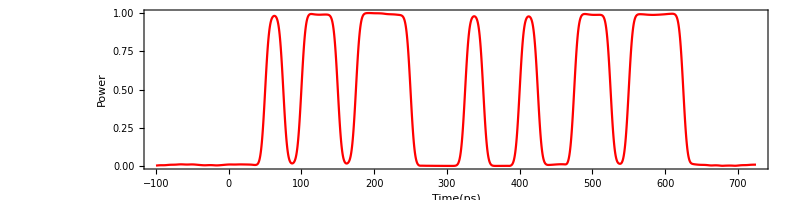

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

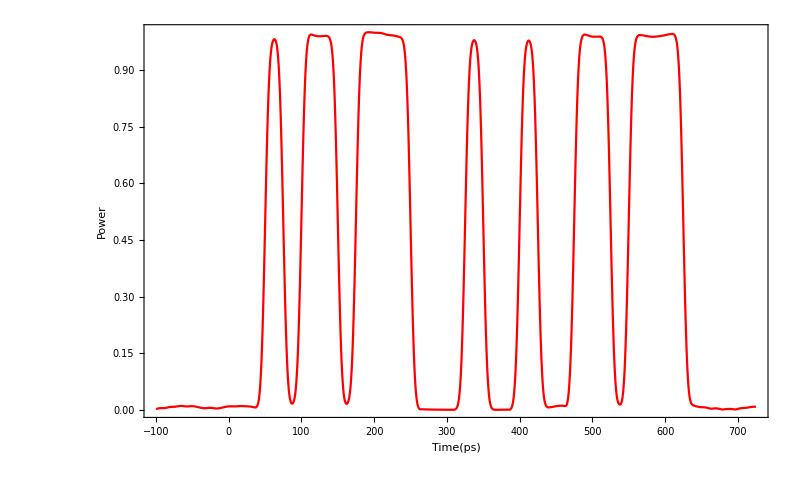

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->40,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

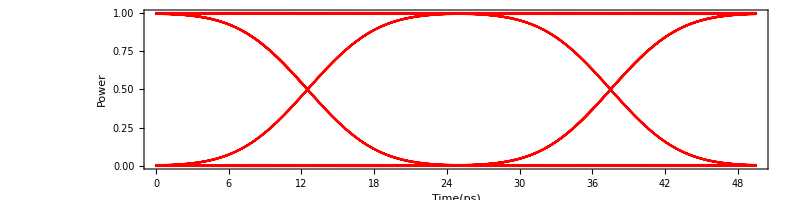

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

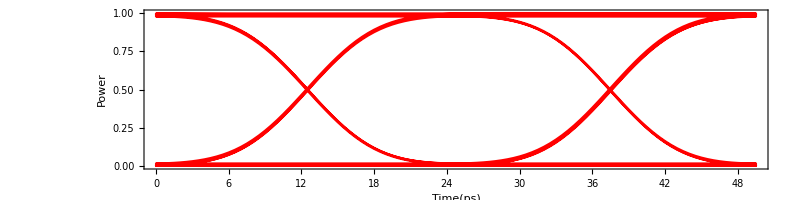

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 66 point

0 is 66 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.986495

Average of 0 is 0.00978253

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.00717472

A Standard Deviation of 0 is 0.00733483

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-1.83621×10^8]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: Exp[-16462.6]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

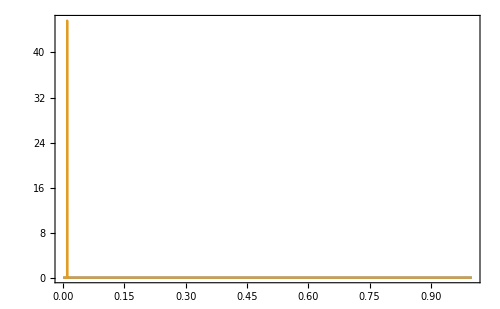

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 67.3151

Q-dB is 36.5623 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.

Eye Opening is 0.985145

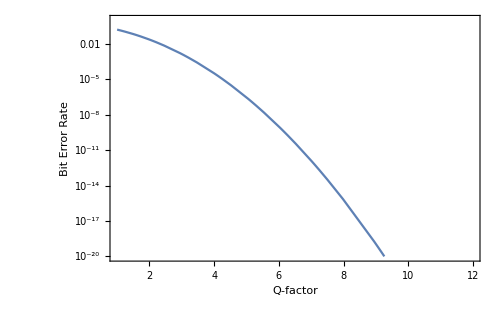

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```